```mathematica
dPhi=500;Tm=100;
```

```mathematica
vbth[deltaPhi_,T_]:=√(deltaPhi/T);
```

```mathematica
normFacMaxwellian[T_,kappa_]:=(m/(2 π T))^(3/2)
```

```mathematica
normFacKappa[T_,kappa_]:=(m/(2 π T (1 - 3/(2 kappa))))^(3/2)Gamma[kappa+1]/(kappa^(3/2)Gamma[kappa-1/2])
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
<<jvFuncs.wl
```

## Distribution functions at source

#### Step function definition

```mathematica
sourcePieceFuncMax[vpar_,vperp_,vbth_,RB_,potExp_]:=Piecewise[{{1,vperp^2(1-RB)+vpar^2+vbth^2>0&&vpar>0},{0,vpar≤ 0},{0,vperp^2(1-RB)+vpar^2+vbth^2≤ 0}}]
```

```mathematica
sourcePieceFuncKappa[vpar_,vperp_,vbth_,RB_]:=Piecewise[{{1,vperp^2(1-RB)+vpar^2+vbth^2>0&&vpar>0},{0,vpar≤ 0},{0,vperp^2(1-RB)+vpar^2+vbth^2≤ 0}}]
```

#### Kappa function definition

Kappa w/ modified step func, in units s.t. v_th=1

```mathematica
sourceFuncMaxwellian[vpar_,vperp_,vbth_,RB_,potExp_]:=1/π^(3/2)Exp[-(vpar^2+vperp^2+vbth^2)]sourcePieceFuncMax[vpar,vperp,vbth,RB,potExp]
```

```mathematica
sourceFuncKappa[vpar_,vperp_,vbth_,RB_,kappa_]:=1/(π^(3/2)(1-3/(2 kappa))^(3/2))Gamma[kappa+1]/(kappa^(3/2)Gamma[kappa-1/2])(1+(vpar^2+vperp^2+vbth^2)/(kappa-3/2))^(-(kappa+1))sourcePieceFuncKappa[vpar,vperp,vbth,RB]
```

## Distribution functions at bottom of potential drop

```mathematica
bottomPieceFuncKappa[vpar_,vperp_,vbth_,RB_]:=Piecewise[{{1,vperp^2(1-1/RB)+vpar^2-vbth^2>0&&vpar>0},{0,vpar≤ 0},{0,vperp^2(1-1/RB)+vpar^2-vbth^2≤ 0}}]
```

```mathematica
bottomPieceFuncKappaRho[rho_,θ_,phiBar_,RB_]:=Piecewise[{{1,rho^2(1- (Sin[θ])^2/RB)-phiBar>0&&rho≥ 0},{0,rho≤ 0},{0,rho^2(1- (Sin[θ])^2/RB)-phiBar< 0}}]
```

```mathematica
bottomPieceFuncMax[vpar_,vperp_,vbth_,RB_,potExp_]:=Piecewise[{{1,vperp^2(1-1/RB)+vpar^2-vbth^2>0&&vpar>0},{0,vpar≤ 0},{0,vperp^2(1-1/RB)+vpar^2-vbth^2≤ 0}}]
```

```mathematica
bottomPieceFuncMaxRho[rho_,θ_,phiBar_,RB_]:=Piecewise[{{1,rho^2(1- (Sin[θ])^2/RB)-phiBar>0&&rho≥ 0},{0,rho≤ 0},{0,rho^2(1- (Sin[θ])^2/RB)-phiBar< 0}}]
```

```mathematica
bottomFuncMaxwellian[vpar_,vperp_,vbth_,RB_,potExp_]:=1/π^(3/2)Exp[-(vpar^2+vperp^2-vbth^2)]bottomPieceFuncMax[vpar,vperp,vbth,RB,potExp]
```

```mathematica
bottomFuncKappa[vpar_,vperp_,vbth_,RB_,kappa_]:=1/(π^(3/2)(1-3/(2 kappa))^(3/2))Gamma[kappa+1]/(kappa^(3/2)Gamma[kappa-1/2])(1+(vpar^2+vperp^2-vbth^2)/(kappa-3/2))^(-(kappa+1))bottomPieceFuncKappa[vpar,vperp,vbth,RB]
```

```mathematica
MaxwellGrate[RB_,phiBar_]:=2/(√π)NIntegrate[rho^2 Sin[theta] Exp[-rho^2+phiBar]bottomPieceFuncMaxRho[rho,theta,phiBar,RB],{theta,0,π/2},{rho,0,20}]
```

```mathematica
kappaFac[RB_,phiBar_,kappa_]:=phiBar^(3/2)/(√π)Gamma[kappa+1]/((kappa-3/2)^(3/2)Gamma[kappa-1/2])(NIntegrate[√(Ebar+1)(1+(Ebar phiBar)/(kappa-3/2))^(-(kappa+1)),{Ebar,0,∞}]-1/(RB-1)NIntegrate[√(1-Ebar)(1+(Ebar phiBar)/((kappa-3/2) (RB-1)))^(-(kappa+1)),{Ebar,0,1}])
```

```mathematica
kappaTest=3;
kString=ToString[StringForm["κ=`1`",kappaTest]];
```

Compare Maxwellian and kappa curves via NIntegration

```mathematica
legends=Style[#,FontSize->20]&/@{"κ=1.55","κ → ∞ (Maxwellian)"}
```

{κ=1.55,κ → ∞ (Maxwellian)}

```mathematica
nDigitsdPhi=3;nDigitsTm=3;
```

```mathematica
{dPhi1,dPhi2}={100,1000};
```

```mathematica
kColors={Black,Blue,Orange};
```

```mathematica
plotStyles=Flatten@Table[Directive[color,lineStyle],{lineStyle,{Thick,Dashed,Dotted}},{color,kColors}];
```

```mathematica
nPlots=6;
```

```mathematica
legends=Style[#,FontSize->20]&/@{"κ=1.6","κ=2.45","κ → ∞ (Maxwellian)"};
If[nPlots>3,legends=legends~Join~Table["",{n,1,nPlots-3}]]
```

{κ=1.6,κ=2.45,κ → ∞ (Maxwellian),,,}

General::munfl: Exp[-4942.31] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-49423.1] is too small to represent as a normalized machine number; precision may be lost.

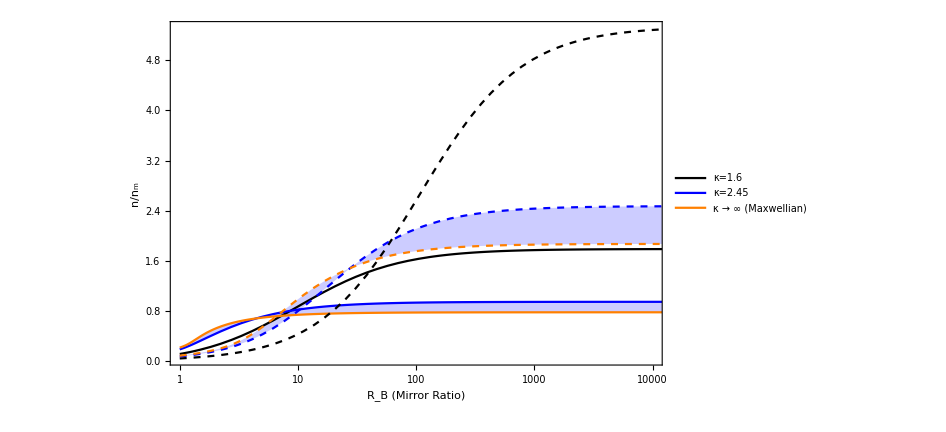

```mathematica
this2=LogLinearPlot[
{nVKappaIntegrate1D[dPhi1,RB,Tm,1,16/10],nVKappaIntegrate1D[dPhi1,RB,Tm,1,245/100],nVMaxwellian[dPhi1,RB,Tm,1],
nVKappaIntegrate1D[dPhi2,RB,Tm,1,16/10],nVKappaIntegrate1D[dPhi2,RB,Tm,1,245/100],nVMaxwellian[dPhi2,RB,Tm,1]},{RB,1,20000},PlotRange->{{1,10000},All},
GridLines->{{10,100,1000},{1,2,3,4,5}},
PlotStyle->plotStyles[[1;;nPlots]],PlotLegends->legends,LabelStyle->(FontSize->22),Frame->True,FrameStyle->Black,FrameLabel->{{StringForm["n/n_m"],""},{StringForm["R_B (Mirror Ratio)"],""}},ImageSize->700,Filling->{{2->{3}},{5->{6}}}]
```

## Now anuvver

```mathematica
{RB1,RB2,RB3,RB4}={3,30,300,1*^6};
```

```mathematica
kColors={Black,Blue,Orange};
```

```mathematica
plotStyles=Flatten@Table[Directive[color,lineStyle],{lineStyle,{Thick,Dashed,Dotted}},{color,kColors}];
```

```mathematica
nPlots=3;
```

```mathematica
legends=Style[#,FontSize->20]&/@{"κ=1.6","κ=2.45","κ → ∞ (Maxwellian)"}
If[nPlots>3,legends=legends~Join~Table["",{n,1,nPlots-3}]];
```

{κ=1.6,κ=2.45,κ → ∞ (Maxwellian)}

```mathematica
RBSinglePlot=RB2;
```

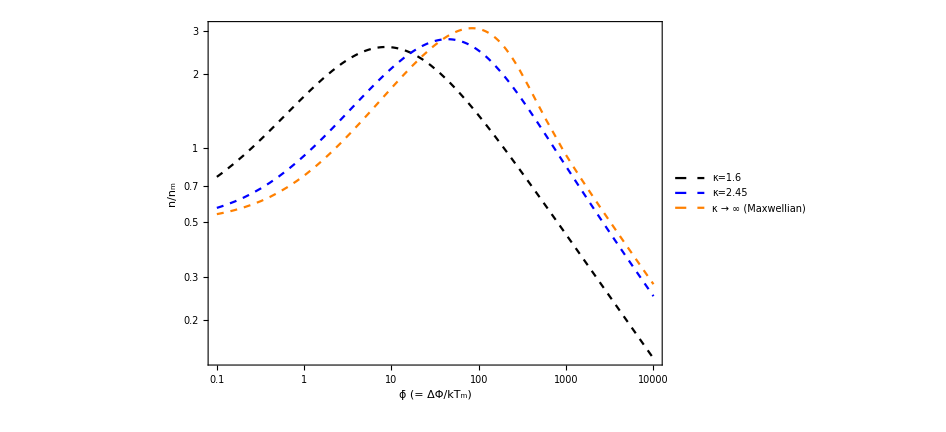

```mathematica
this2=LogLogPlot[
{kappaFac[RBSinglePlot,phiBar,16/10],kappaFac[RBSinglePlot,phiBar,245/100],LKMwellDensFac[phiBar,RBSinglePlot]},{phiBar,0.1,10000},PlotRange->{All,All},PlotStyle->plotStyles[[1;;nPlots]],PlotLegends->legends,LabelStyle->(FontSize->22),Frame->True,FrameStyle->Black,FrameLabel->{{StringForm["n/n_m"],""},{StringForm["ϕ̄ (= ΔΦ/kT_m)"],""}},ImageSize->700]
```

```mathematica
nPlots=9;
```

```mathematica
legends=Style[#,FontSize->20]&/@{"κ=1.6","κ=2.45","κ → ∞ (Maxwellian)"}
If[nPlots>3,legends=legends~Join~Table["",{n,1,nPlots-3}]];
```

{κ=1.6,κ=2.45,κ → ∞ (Maxwellian)}

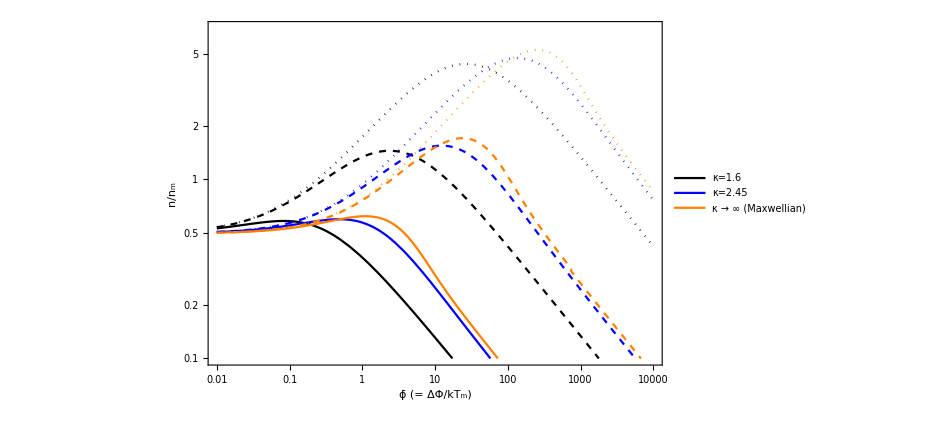

```mathematica
this2=LogLogPlot[
{kappaFac[RB1,phiBar,16/10],kappaFac[RB1,phiBar,245/100],LKMwellDensFac[phiBar,RB1],
kappaFac[RB2,phiBar,16/10],kappaFac[RB2,phiBar,245/100],LKMwellDensFac[phiBar,RB2],
kappaFac[RB3,phiBar,16/10],kappaFac[RB3,phiBar,245/100],LKMwellDensFac[phiBar,RB3]},{phiBar,0.01,10000},PlotRange->{All,{0.1,7}},
GridLines->{{0.1,1,10,100,1000},{0.2,0.5,1,2,5}},
PlotStyle->plotStyles[[1;;nPlots]],PlotLegends->legends,LabelStyle->(FontSize->22),Frame->True,FrameStyle->Black,FrameLabel->{{StringForm["n/n_m"],""},{StringForm["ϕ̄ (= ΔΦ/kT_m)"],""}},ImageSize->700]
```

```mathematica
this2=LogLogPlot[
{kappaFac[RBSinglePlot,phiBar,16/10],kappaFac[RBSinglePlot,phiBar,245/100],LKMwellDensFac[phiBar,RBSinglePlot]},{phiBar,0.1,10000},PlotRange->{All,All},PlotStyle->plotStyles[[1;;nPlots]],PlotLegends->legends,LabelStyle->(FontSize->22),Frame->True,FrameStyle->Black,FrameLabel->{{StringForm["n/n_m"],""},{StringForm["ϕ̄ (= ΔΦ/kT_m)"],""}},ImageSize->700]
```

```mathematica
this2=LogLinearPlot[
{kappaGrate[RB1,phiBar,16/RB1],kappaGrate[RB1,phiBar,245/100],MaxwellGrate[RB1,phiBar],
kappaGrate[10,phiBar,16/10],kappaGrate[RB2,phiBar,245/100],MaxwellGrate[RB2,phiBar],
kappaGrate[RB3,phiBar,16/10],kappaGrate[RB3,phiBar,245/100],MaxwellGrate[RB3,phiBar],
kappaGrate[RB4,phiBar,16/10],kappaGrate[RB4,phiBar,245/100],MaxwellGrate[RB4,phiBar]},{phiBar,1,10000},PlotRange->{All,All},PlotLegends->legends,LabelStyle->(FontSize->22),Frame->True,FrameLabel->{{StringForm["n/n_m"],""},{StringForm["Mirror Ratio R_B"],""}},ImageSize->700]
```